# 2D global conformal block demo

```mathematica
(*** Define projective lightcone variables for the four operators ***)
Do[X[i]=Table[x[i,j],{j,1,4}],{i,1,4}];

(*** Lorentzian inner product on the auxiliary R^(3,1) space ***)
Inn[Y_,Z_]:=-Y[[1]] Z[[1]]+Sum[Y[[i]] Z[[i]],{i,2,4}]  

(*** Note that at this stage we haven't yet restricted to the lightcone ***)

(*** The scalar 4-point conformal block, expressed in terms of G[u,v] ***)
FourPointFunction=Inn[X[1],X[2]]^(-(Δ1+Δ2)/2) Inn[X[3],X[4]]^(-(Δ3+Δ4)/2) (Inn[X[2],X[4]]/Inn[X[1],X[4]])^((Δ1-Δ2)/2)(Inn[X[1],X[4]]/Inn[X[1],X[3]])^((Δ3-Δ4)/2) G[Inn[X[1],X[2]] Inn[X[3],X[4]]/(Inn[X[1],X[3]] Inn[X[2],X[4]]),Inn[X[1],X[4]] Inn[X[2],X[3]]/(Inn[X[1],X[3]] Inn[X[2],X[4]])];

(*** Define the conformal generators L[i,j] in projective lightcone representation, acting on the first two fields in the 4-point function, with coordinates X[1] and X[2] ***)
L[i_,j_][f_]:=If[i==1,-1,1] (x[1,i] D[f,x[1,j]]+x[2,i] D[f,x[2,j]])-If[j==1,-1,1] (x[1,j] D[f,x[1,i]]+x[2,j] D[f,x[2,i]])

(*** L2[f] is minus the Casimir operator, L^2=1/2 L^AB Subscript[L, AB], acting on the function f ***)
L2[f_]:=1/2 Sum[If[i==1,-1,1] If[j==1,-1,1] L[i,j][L[i,j][f]],{i,1,4},{j,1,4}]

(*** We will set X[1]={1,1,0,0}, X[2]={(1+a^2+b^2)/2,(1-a^2-b^2)/2,a,b}, X[3]={1,0,1,0}, X[4]={(1+ϵ^-2)/2,(1-ϵ^-2)/2,0,1/ϵ} ***)
CoordinateSubstitution={x[1,1]->1,x[1,2]->1,x[1,3]->0,x[1,4]->0,x[2,1]->(1+a^2+b^2)/2,x[2,2]->(1-a^2-b^2)/2,x[2,3]->a,x[2,4]->b,x[3,1]->1,x[3,2]->0,x[3,3]->1,x[3,4]->0,x[4,1]->(1+1/ϵ^2)/2,x[4,2]->(1-1/ϵ^2)/2,x[4,3]->0,x[4,4]->1/ϵ};
(*** After taking ϵ to zero limit, (a,b) will be related to z by z=a+ib ***)

(*** This expression is supposed to be equal to be the Casimir eigenvalue when acting on the conformal block ***)
Casimir=Assuming[a>0 && b>0 && ϵ>0 && Δ1>0 && Δ2>0 && Δ3>0 && Δ4>0,(-L2[FourPointFunction]/FourPointFunction/.CoordinateSubstitution//Simplify)/.ϵ->0]
```

a (Δ1-Δ2) (Δ3-Δ4)+1/G[a^2+b^2,1-2 a+a^2+b^2]2 ((-a^2+a^3+b^2+a b^2) (-2+Δ1-Δ2-Δ3+Δ4) G^(0,1)[a^2+b^2,1-2 a+a^2+b^2]-2 (1-2 a+a^2+b^2) (-a^2+a^3+b^2+a b^2) G^(0,2)[a^2+b^2,1-2 a+a^2+b^2]+(a^2+b^2) (a (-2+Δ1-Δ2-Δ3+Δ4) G^(1,0)[a^2+b^2,1-2 a+a^2+b^2]-2 (2 a (1-2 a+a^2+b^2) G^(1,1)[a^2+b^2,1-2 a+a^2+b^2]+(-1+a) (a^2+b^2) G^(2,0)[a^2+b^2,1-2 a+a^2+b^2])))

```mathematica
(*** Changing variables, from G[u,v] to F[z,zbar] ***)
G[u_,v_]:=F[1/2 (1+u+√(-4 u+(1+u-v)^2)-v),1/2 (1+u-√(-4 u+(1+u-v)^2)-v)]
(*** verifying that the change of coordinate is correct ***)
Assuming[b>0,G[a^2+b^2,1-2 a+a^2+b^2]//Simplify]
```

F[a+ⅈ b,a-ⅈ b]

```mathematica
(*** Casimir eigenvalue, now expressed in terms of F[z,zbar] ***)
CasimirZ=Assuming[b>0,(Casimir//Simplify)/.{a->(z+zbar)/2,b->(z-zbar)/(2I)}//Simplify]
```

1/2 (z+zbar) (Δ1-Δ2) (Δ3-Δ4)-1/F[z,zbar](zbar^2 (2-Δ1+Δ2+Δ3-Δ4) F^(0,1)[z,zbar]+2 (-1+zbar) zbar^2 F^(0,2)[z,zbar]+z^2 ((2-Δ1+Δ2+Δ3-Δ4) F^(1,0)[z,zbar]+2 (-1+z) F^(2,0)[z,zbar]))

```mathematica
(*** Checking the leading term in the conformal block from OPE ***)
H[z_,zbar_]:=z^((Δ+s)/2) zbar^((Δ-s)/2)

((CasimirZ/.F->H)//Simplify)/.{z->0,zbar->0}//Simplify
```

s^2+(-2+Δ) Δ

```mathematica
(*** The 2D scalar conformal block ***)
Block2D[z_,zbar_]:=z^((Δ+s)/2) zbar^((Δ-s)/2) Hypergeometric2F1[(Δ+s)/2-(Δ1-Δ2)/2,(Δ+s)/2+(Δ3-Δ4)/2,Δ+s,z] Hypergeometric2F1[(Δ-s)/2-(Δ1-Δ2)/2,(Δ-s)/2+(Δ3-Δ4)/2,Δ-s,zbar]

(*** Checking that it has the correct Casimir by Taylor expansion in z, zbar ***)
(CasimirZ-(s^2+(-2+Δ) Δ)/.F->Block2D/.{z->ϵ z,zbar->ϵ zbar}/.{Hypergeometric2F1[a_,b_,c_,ϵ x_]:>(Hypergeometric2F1[a,b,c,ϵ x]+O[ϵ]^4)})//Simplify

(*** Checking that it has the correct Casimir by plugging in random numerical values ***)
CasimirZ-(s^2+(-2+Δ) Δ)/.F->Block2D/.{z->.3,zbar->.4,Δ->1.3,s->1,Δ1->1.7,Δ2->1.8,Δ3->1.22,Δ4->1.25}
```

O[ϵ]^2

-5.55112×10^-17

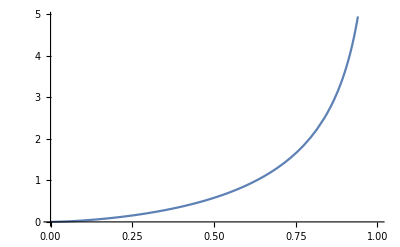

```mathematica
(*** testing numerical values of the conformal block itself ***)
Plot[(Block2D[x,x])/.{Δ1->1/8,Δ2->1/8,Δ3->1/8,Δ4->1/8,Δ->1.5,s->0},{x,0,1}]
```

```mathematica
(*** After setting Δ1=Δ2=Δ3=Δ4, contribution to the crossing equation, v^Δ1 F[u,v]-u^Δ1 F[v,u] ***)
CrossingBlock[z_,zbar_]=(1-z)^Δ1(1-zbar)^Δ1 Block2D[z,zbar]-z^Δ1 zbar^Δ1 Block2D[1-z,1-zbar]/.{Δ2->Δ1,Δ3->Δ1,Δ4->Δ1}//Simplify
```

-(1-z)^((s+Δ)/2) z^Δ1 (1-zbar)^(1/2 (-s+Δ)) zbar^Δ1 Hypergeometric2F1[1/2 (-s+Δ),1/2 (-s+Δ),-s+Δ,1-zbar] Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,1-z]+(1-z)^Δ1 z^((s+Δ)/2) (1-zbar)^Δ1 zbar^(1/2 (-s+Δ)) Hypergeometric2F1[1/2 (-s+Δ),1/2 (-s+Δ),-s+Δ,zbar] Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,z]

```mathematica
(*** Extracting the x and x^3 terms in the z=zbar=1/2+x expansion of CrossingBlock ***)
P2D:=(series=CrossingBlock[1/2+x,1/2+x]+O[x]^4//N;{SeriesCoefficient[series,1],SeriesCoefficient[series,3]})
```

```mathematica
(*** Some numerical values of P2D, with Δ1=2, at different values of Δ, spin s=0 ***)
Table[{weight,P2D/.{Δ1->1/8,Δ->weight,s->0}},{weight,0,6,1}]
```

{{0,{-0.840896,-0.735784}},{1,{2.82797,1.4022}},{2,{4.25891,11.8744}},{3,{4.51045,34.9042}},{4,{4.18412,64.2365}},{5,{3.61833,92.7435}},{6,{2.99564,115.561}}}

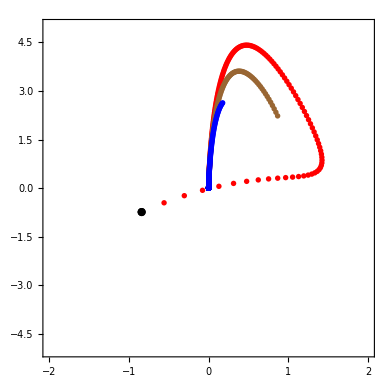

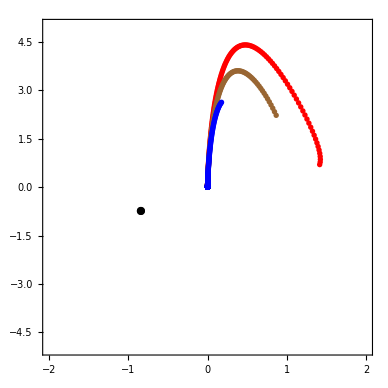

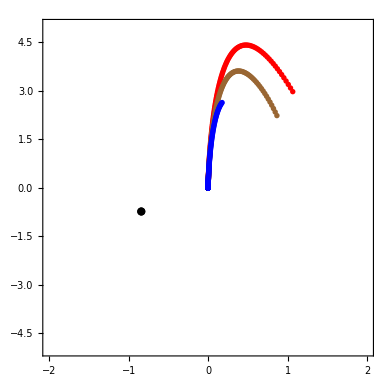

```mathematica
maxweight=30;weightstep=0.05;
PlotP2D[weight1_,spin_,gap_,color_]:=ListPlot[Table[P2D/1.1^(spin)/2^weight/.{Δ1->weight1,Δ->weight,s->spin},{weight,Max[spin,gap],maxweight,weightstep}],PlotRange->{2{-1,1},5{-1,1}},AspectRatio->1,Axes->True,Frame->True,PlotStyle->{PointSize[.01],color}]
PlotIdentity[weight1_]:=ListPlot[{P2D/.{Δ1->weight1,Δ->0,s->0}},PlotRange->{5{-1,1},50{-1,1}},AspectRatio->1,Axes->True,Frame->True,PlotStyle->{PointSize[.015],Black}]

GapPlot[weight1_,gap_]:=Show[PlotP2D[weight1,0,gap,Red],PlotP2D[weight1,2,0,Brown],PlotP2D[weight1,4,0,Blue],PlotIdentity[weight1]]

(*** Plotting the order x and x^3 components of CrossingBlock (suitably rescaled for visualization) for external weight Δ1=1/8, a range of internal weight Δ, spin s=0,2,4 (in red, brown, blue) with scalar gap 0, 1, and 2 respectively ***)
GapPlot[1/8,0]
GapPlot[1/8,1]
GapPlot[1/8,2]
```

# 4D conformal blocks demo (scalar external primaries)

```mathematica
(*** DD is the differential operator that, when acting on the 4D scalar block, gives one half of the SO(5,1) Casimir ***)
DD[f_]:=z^2(1-z) D[f,{z,2}]+((Δ1-Δ2-Δ3+Δ4)/2 -1) z^2 D[f,z]+(Δ1-Δ2)(Δ3-Δ4)/4 z f+2 z zbar/(z-zbar)(1-z) D[f,z]+zbar^2(1-zbar) D[f,{zbar,2}]+((Δ1-Δ2-Δ3+Δ4)/2 -1) zbar^2 D[f,zbar]+(Δ1-Δ2)(Δ3-Δ4)/4 zbar f+2 z zbar/(zbar-z)(1-zbar) D[f,zbar]

(*** DD0 is a new differential operator that splits into a holomorphic part and an anti-holomorphic part, whereas DD doesn't  ***)
DD0[f_]:=z^2(1-z) D[f,{z,2}]+((Δ1-Δ2-Δ3+Δ4)/2 +1) z^2 D[f,z]-2z D[f,z]+(Δ1-Δ2+2)(Δ3-Δ4-2)/4 z f+zbar^2(1-zbar) D[f,{zbar,2}]+((Δ1-Δ2-Δ3+Δ4)/2 +1) zbar^2 D[f,zbar]-2zbar D[f,zbar]+(Δ1-Δ2+2)(Δ3-Δ4-2)/4 zbar f

(*** checking that DD and DD0 are related by DD 1/(z-zbar) = 1/(z-zbar)(DD0+2) ***)
DD[f[z,zbar]/(z-zbar)] -1/(z-zbar) (DD0[f[z,zbar]]+2f[z,zbar])//Simplify
```

0

```mathematica
(*** The 4D scalar conformal block ***)
Block4D[z_,zbar_]:=z^((Δ+s)/2+1) zbar^((Δ-s)/2)/(z-zbar) Hypergeometric2F1[(Δ+s)/2-(Δ1-Δ2)/2,(Δ+s)/2+(Δ3-Δ4)/2,Δ+s,z] Hypergeometric2F1[(Δ-s)/2-(Δ1-Δ2)/2-1,(Δ-s)/2+(Δ3-Δ4)/2-1,Δ-s-2,zbar]+zbar^((Δ+s)/2+1) z^((Δ-s)/2)/(zbar-z) Hypergeometric2F1[(Δ+s)/2-(Δ1-Δ2)/2,(Δ+s)/2+(Δ3-Δ4)/2,Δ+s,zbar] Hypergeometric2F1[(Δ-s)/2-(Δ1-Δ2)/2-1,(Δ-s)/2+(Δ3-Δ4)/2-1,Δ-s-2,z] 

(*** testing that the equation Casimir = Δ(Δ-4)+s(s+2) is obeyed by Taylor expansion in z, zbar ***)
(DD[Block4D[z, zbar]]/((Δ(Δ-4)+s(s+2))/2  Block4D[z, zbar])/.{Δ2->Δ1,Δ4->Δ3}/.{Δ->3,s->0}/.{z->ϵ z,zbar->ϵ zbar})+O[ϵ]^4//Simplify
(DD[Block4D[z, zbar]]/((Δ(Δ-4)+s(s+2))/2  Block4D[z, zbar])/.{Δ2->Δ1,Δ4->Δ3}/.{Δ->5,s->2}/.{z->ϵ z,zbar->ϵ zbar})+O[ϵ]^4//Simplify

(*** Testing the Casimir equation by plugging in random numerical values ***)
DD[Block4D[z,zbar]]-1/2 (Δ(Δ-4)+s(s+2)) Block4D[z,zbar]/.{Δ1->2,Δ2->2,Δ3->2,Δ4->2,Δ->3,s->0,z->.4+.5 I,zbar->.5-.3 I}
```

1+O[ϵ]^4

1+O[ϵ]^4

-1.11022×10^-16-1.11022×10^-16 ⅈ

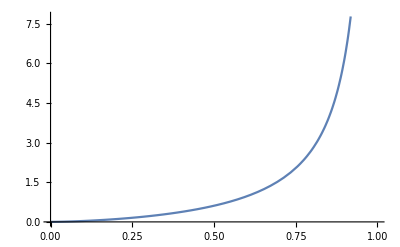

```mathematica
(*** testing numerical values of the conformal block itself ***)
Plot[(Block4D[x+.001I,x-.001I]//Re)/.{Δ1->2,Δ2->2,Δ3->2,Δ4->2,Δ->1.5,s->0},{x,0,1}]
```

```mathematica
(*** After setting Δ1=Δ2=Δ3=Δ4, contribution to the crossing equation, v^Δ1 F[u,v]-u^Δ1 F[v,u], multiplied by (z-zbar) ***)
CrossingBlock[z_,zbar_]=(z-zbar)(1-z)^Δ1(1-zbar)^Δ1 Block4D[z,zbar]-(z-zbar)z^Δ1 zbar^Δ1 Block4D[1-z,1-zbar]/.{Δ2->Δ1,Δ3->Δ1,Δ4->Δ1}//Simplify
```

(1-z)^(1/2 (-s+Δ)) z^Δ1 (1-zbar)^(1/2 (-s+Δ)) zbar^Δ1 ((1-z)^(1+s) Hypergeometric2F1[1/2 (-2-s+Δ),1/2 (-2-s+Δ),-2-s+Δ,1-zbar] Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,1-z]+(1-zbar)^s (-1+zbar) Hypergeometric2F1[1/2 (-2-s+Δ),1/2 (-2-s+Δ),-2-s+Δ,1-z] Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,1-zbar])+(1-z)^Δ1 z^(1/2 (-s+Δ)) (1-zbar)^Δ1 zbar^(1/2 (-s+Δ)) (z^(1+s) Hypergeometric2F1[1/2 (-2-s+Δ),1/2 (-2-s+Δ),-2-s+Δ,zbar] Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,z]-zbar^(1+s) Hypergeometric2F1[1/2 (-2-s+Δ),1/2 (-2-s+Δ),-2-s+Δ,z] Hypergeometric2F1[(s+Δ)/2,(s+Δ)/2,s+Δ,zbar])

```mathematica
(*** Extracting the x^m xbar^n terms in the z=1/2+x expansion of CrossingBlock, for m+n=even (recall that we have multiplied by an extra (z-zbar) factor) ***)
CrossingDeriv[weight1_,weight_,spin_,deg_]:=Block[{mat=CoefficientList[((CrossingBlock[1/2+ϵ x,1/2+ϵ xbar]/.{Δ1->weight1,Δ->weight,s->spin})+O[ϵ]^(2 deg+1)//Normal//N)/.ϵ->1,{x,xbar}]},Sum[A[m,n] mat[[m+1,n+1]],{m,0,2 deg},{n,m+2,2 deg-m,2}]//Flatten]

(*** Collecting the Taylor-expanded crossing equations for spins up to spintrunc, weights from the unitarity bound or scalar gap up to weighttrunc, with sufficiently small weightstep ***)
PrepareCoeff[Δ1_,gap_,weighttrunc_,weightstep_,spintrunc_,deg_]:=Join[{CrossingDeriv[Δ1,0,0,deg]},Table[CrossingDeriv[Δ1,Δ,spin,deg],{spin,0,spintrunc,2},{Δ,If[spin==0,gap,2+spin],weighttrunc,weightstep}]//Flatten]

(*** Coefficients of the linear functional as variables for linear optimization ***)
vars[deg_]:=Table[A[m,n],{m,0,2 deg},{n,m+2,2 deg-m,2}]//Flatten;

(*** total derivative order on the crossing equation is effectively 2 times derivatives - 1 ***)
derivatives=4; 

(*** Numerical approximations are introduced here via cutoff on the spin, internal weight, and discretization of possible weight values; the need for cutoff and discretization of weights can be removed with "polynomial matrix programming", but we won't implement it here ***)
maxweight=12;
stepweight=.05;
maxspin=8;

(*** normalizing one of the linear functional coefficients so that the optimization problem can have a well-defined solution ***)
normalization=vars[derivatives][[1]];
normvars=Drop[vars[derivatives],1];

blockcoeffs[Δ1_,gap_]:=PrepareCoeff[Δ1,gap,maxweight,stepweight,maxspin,derivatives]/.normalization->1

(*** oracle tells whether the gap is allowed (true) or not allowed (false)***)
oracle[Δ1_,gap_]:=Block[{MM=blockcoeffs[Δ1,gap]},(normvars[[1]]/.LinearOptimization[MM[[1]],#≥0 & /@ MM,normvars])===Indeterminate]
```

```mathematica
oracle[1.05,2.53]
oracle[1.05,2.54]
```

True

False

# 3D conformal block demo (scalar external primaries)

```mathematica
(*** General d scalar conformal block from Zamolodchikov recursion relation (code by Joshua Sandor) ***)
hIn[l_,r_,η_,d_]:= (l! GegenbauerC[l,(d-2)/2,η])/((-2)^l Pochhammer[d/2-1,l](1-r^2)^((d-2)/2)√((1+r^2)^2-4 r^2 η^2))
c[1,m_,l_,d_]:= -(m(-2)^m)/(m!)^2 Pochhammer[(1-m)/2,m]^2
c[2,m_,l_,d_]:= -(m l!Pochhammer[d/2+l,-m]Pochhammer[d/2+l-1,-m])/((-2)^m(m!)^2(l-m)!Pochhammer[d-2+l,-m])Pochhammer[(1-m)/2,m]^2
c[3,m_,l_,d_]:= -((m(-1)^(m/2)Pochhammer[(d-m)/2-1,m])/(2((m/2)!)^2 Pochhammer[(d-m)/2+l-1,m]Pochhammer[(d-m)/2+l,m]))Pochhammer[(2-(d+m)/2-l)/2,m/2]^2 Pochhammer[((d-m)/2+l)/2,m/2]^2
Δ[1,m_,l_,d_]:= 1-l-m
Δ[2,m_,l_,d_]:= l+d-1-m
Δ[3,m_,l_,d_]:= (d-m)/2
ll[1,m_,l_,d_]:= l+m
ll[2,m_,l_,d_]:= l-m
ll[3,m_,l_,d_]:= l
MaxOrder = 30;
hInExpansion[d_,l_]:=hInExpansion[d,l]  = Table[SeriesCoefficient[ Series[hIn[l,r,η,d],{r,0,MaxOrder}],n],{n,0,MaxOrder}];
(*order needs to be even!*)
RecursiveBlock[0,Δb_, lb_,d_]:=RecursiveBlock[0,Δb, lb,d]= hInExpansion[d,lb][[1]]
RecursiveBlock[ord_,Δb_, lb_,d_]:=RecursiveBlock[ord,Δb, lb,d]= Module[{hinf,J1, J2, J3},
hinf = Sum[hInExpansion[d,lb][[ii]] r^(ii-1),{ii,1,ord+1}];
J1 = Sum[(c[1,2k,lb,d](4r)^(2k))/(Δb- Δ[1,2k,lb,d])RecursiveBlock[ord-2k,Δ[1,2k,lb,d]+2k,ll[1,2k,lb,d],d],{k,1,ord/2}];
J3= Sum[(c[3,2k,lb,d](4r)^(2k))/(Δb-Δ[3,2k,lb,d])(RecursiveBlock[ord-2k,Δ[3,2k,lb,d]+2k,ll[3,2k,lb,d],d]),{k,1,ord/2}];
If[lb>= 2,
J2 = Sum[(c[2,2k,lb,d](4r)^(2k))/(Δb- Δ[2,2k,lb,d])RecursiveBlock[ord-2k,Δ[2,2k,lb,d]+2k,ll[2,2k,lb,d],d],{k,1,Min[ord/2,lb/2]}];
,J2 = 0];
Return[Simplify[hinf+J1+ J2+ J3]]
]
RecursiveBlockPoleExp[0,Δb_, lb_,d_]:=RecursiveBlockPoleExp[0,Δb, lb,d]= hInExpansion[d,lb][[1]]
RecursiveBlockPoleExp[ord_,Δb_, lb_,d_]:=RecursiveBlockPoleExp[ord,Δb, lb,d]= Module[{hinf,J1, J2, J3},
hinf = Sum[hInExpansion[d,lb][[ii]] r^(ii-1),{ii,1,ord+1}];
J1 = Sum[c[1,2k,lb,d](4r)^(2k)Pole[Δb,Δ[1,2k,lb,d]]RecursiveBlock[ord-2k,Δ[1,2k,lb,d]+2k,ll[1,2k,lb,d],d],{k,1,ord/2}];
J3= Sum[c[3,2k,lb,d](4r)^(2k)Pole[Δb,Δ[3,2k,lb,d]](RecursiveBlock[ord-2k,Δ[3,2k,lb,d]+2k,ll[3,2k,lb,d],d]),{k,1,ord/2}];
If[lb>= 2,
J2 = Sum[c[2,2k,lb,d](4r)^(2k)Pole[Δb, Δ[2,2k,lb,d]]RecursiveBlock[ord-2k,Δ[2,2k,lb,d]+2k,ll[2,2k,lb,d],d],{k,1,Min[ord/2,lb/2]}];
,J2 = 0];
Return[Simplify[hinf+J1+ J2+ J3]]
]
RecursiveG[ord_,Δb_, lb_,d_]:= (4r)^Δb RecursiveBlock[ord,Δb, lb,d]
```

```mathematica
(*** The general d conformal block with external weight factor stripped off, first for scalar intermediate primary, and then general internal spin recursively. This is slow but serves as a check for the Zamolodchikov recursion ***)
slowG[d_,Δ_,0,z_,zbar_,trunc_]:=Block[{u=z zbar,v=(1-z)(1-zbar)},u^(Δ/2) Sum[Pochhammer[Δ/2,m]^2 Pochhammer[Δ/2,(m+n)]^2/(m! n! Pochhammer[Δ+1-d/2,m] Pochhammer[Δ,2m+n]) u^m (1-v)^n,{m,0,trunc},{n,0,trunc}]]

beta[p_]:=p^2/(4(2p-1)(2p+1))

slowG[d_,Δ_,s_,z_,zbar_,trunc_]:=Block[{a=d/2-1},(1/2 (Δ+s-2a-2) (1/z+1/zbar-1) slowG[d,Δ+1,s-1,z,zbar,trunc]+(1-z)D[slowG[d,Δ+1,s-1,z,zbar,trunc],z]+(1-zbar) D[slowG[d,Δ+1,s-1,z,zbar,trunc],zbar]-(s-1)(Δ(Δ-2a+1)/((Δ-a)(Δ-a+1)) beta[1/2(Δ-s+2-2a)] slowG[d,Δ+2,s-2,z,zbar,trunc]+(Δ+s-1)/(s+a-1) slowG[d,Δ,s-2,z,zbar,trunc]))/((Δ-a)(s+2a-1)/(s+a-1)) ]/;s≥1

(*** Conversion between r, η and z, zbar ***)
subs={r->Sqrt[z zbar]/((1+Sqrt[1-z])(1+Sqrt[1-zbar])),
η->(z/(1+Sqrt[1-z])^2+zbar/(1+Sqrt[1-zbar])^2)/(2Sqrt[z zbar]/((1+Sqrt[1-z])(1+Sqrt[1-zbar])))};
```

```mathematica
(*** testing in 3D case ***)
block1=Assuming[x>0 && y>0 && ϵ>0,(RecursiveG[10,Δ,2,3]/r^Δ/.subs/.{z->ϵ x,zbar->ϵ y})+O[ϵ]^5];
block2=Assuming[x>0 && y>0 && ϵ>0,(slowG[3,Δ,2,z,zbar,6]/r^Δ/.subs//.{z->ϵ x,zbar->ϵ y})+O[ϵ]^5];
(*** compare Zamolodchikov recursion against spin recursion, in the spin 2 case (overall constant normalization factor is a matter of convention) ***)
block1/block2//Simplify
```

2/3+O[ϵ]^5

## 3D conformal bootstrap bounding gap

```mathematica
Crossing[Δ1_,Δ_,s_,x_,y_,trunc_]:=(((1-z)^Δ1(1-zbar)^Δ1 RecursiveG[20,Δ,s,3]/.subs/.{z->1/2+ϵ x,zbar->1/2+ϵ y})+O[ϵ]^trunc//Normal)/.ϵ->1

CrossingDeriv[Δ1_,Δ_,s_,deg_,trunc_]:=Block[{x,y,mat=CoefficientList[Crossing[Δ1,Δ,s,x,y,trunc],{x,y}]},Sum[A[m,n] mat[[m+1,n+1]],{m,0,deg},{n,m+1,deg-m,2}]//Flatten]

PrepareCoeff[Δ1_,gap_,weighttrunc_,weightstep_,spintrunc_,deg_,trunc_]:=Block[{h},Monitor[Join[{CrossingDeriv[Δ1,0,0,deg,trunc]},Table[CrossingDeriv[Δ1,h,spin,deg,trunc],{spin,0,spintrunc,2},{h,If[spin==0,gap,1+spin],weighttrunc,weightstep}]//Flatten],{h,spin}]]

vars[deg_]:=Table[A[m,n],{m,0,deg},{n,m+1, deg-m,2}]//Flatten;

derivatives=7;

maxweight=8;
stepweight=.2;
maxspin=6;

truncationlevel=9;

normalization=vars[derivatives][[1]];
normvars=Drop[vars[derivatives],1];

blockcoeffs[Δ1_,gap_]:=PrepareCoeff[Δ1,gap,maxweight,stepweight,maxspin,derivatives,truncationlevel]/.normalization->1

oracle[Δ1_,gap_]:=Block[{MM=blockcoeffs[Δ1,gap]},(normvars[[1]]/.LinearOptimization[MM[[1]],#≥0 & /@ MM,normvars])===Indeterminate]
```

```mathematica
oracle[.518,1.427]
```

LinearOptimization::nsolc: There are no points that satisfy the constraints.

True

```mathematica
oracle[.518,1.428]
```

False

## 3D conformal bootstrap bounding OPE coefficient of the stress tensor

```mathematica
PrepareOPEbound[Δ1_,gap_,weighttrunc_,weightstep_,spintrunc_,deg_,trunc_]:=Block[{h},Monitor[Table[CrossingDeriv[Δ1,h,spin,deg,trunc],{spin,0,spintrunc,2},{h,If[spin==0,gap,1+spin],weighttrunc,weightstep}]//Flatten,{h,spin}]]

derivatives=8;
maxweight=9;
stepweight=.1;
maxspin=8;
truncationlevel=9;

AllVars=vars[derivatives];

OPEboundcoeffs[Δ1_,gap_]:=PrepareOPEbound[Δ1,gap,maxweight,stepweight,maxspin,derivatives,truncationlevel]

NormalizationCondition[Δ1_]:=CrossingDeriv[Δ1,3,2,derivatives,truncationlevel];
MinimizationObjective[Δ1_]:=-CrossingDeriv[Δ1,0,0,derivatives,truncationlevel];

OPEbound[Δ1_,gap_]:=OPEbound[Δ1,gap]=Block[{MM=OPEboundcoeffs[Δ1,gap]},MinimizationObjective[Δ1]/.LinearOptimization[MinimizationObjective[Δ1],Join[#≥0 & /@ MM,{NormalizationCondition[Δ1]==1}],AllVars]]

UnnormalizedCTbound[Δ1_,gap_]:=Δ1^2/OPEbound[Δ1,gap]
```

```mathematica
UnnormalizedCTbound[.518,1.]
UnnormalizedCTbound[.5,1.]
```

0.621795

0.65922

```mathematica
UnnormalizedCTbound[.518,1.]/UnnormalizedCTbound[.5,1.]
```

0.943229